# Manifold at q=6 cycles

## Solver

Solver to identify the coefficients with respect to the free parameter

## Coefficient polynomial structure

```mathematica
ClearAll[alpha,beta,gamma1,gamma2,gamma3,gamma4,gamma5,gamma6,a1,a2,a3,a4,b1,b2,b3];
alpha[a1_,a2_,a3_,b1_,b2_]:=With[{a4=1-a1-a2-a3,b3=1-b1-b2},8.33333*10^-2 a1^2*b1-8.33333*10^-2 a1*a2*b1-8.33333*10^-2 a1*a3*b1-8.33333*10^-2 a1*a4*b1-4.16667*10^-2 a2^2*b1-8.33333*10^-2 a2*a3*b1-8.33333*10^-2 a2*a4*b1-4.16667*10^-2 a3^2*b1-8.33333*10^-2 a3*a4*b1-4.16667*10^-2 a4^2*b1+8.33333*10^-2 a1^2*b2+1.66667*10^-1 a1*a2*b2-8.33333*10^-2 a1*a3*b2-8.33333*10^-2 a1*a4*b2+8.33333*10^-2 a2^2*b2-8.33333*10^-2 a2*a3*b2-8.33333*10^-2 a2*a4*b2-4.16667*10^-2 a3^2*b2-8.33333*10^-2 a3*a4*b2-4.16667*10^-2 a4^2*b2+8.33333*10^-2 a1^2*b3+1.66667*10^-1 a1*a2*b3+1.66667*10^-1 a1*a3*b3-8.33333*10^-2 a1*a4*b3+8.33333*10^-2 a2^2*b3+1.66667*10^-1 a2*a3*b3-8.33333*10^-2 a2*a4*b3+8.33333*10^-2 a3^2*b3-8.33333*10^-2 a3*a4*b3-4.16667*10^-2 a4^2*b3
-4.16667*10^-2 a1*b1^2+8.33333*10^-2 a2*b1^2+8.33333*10^-2 a3*b1^2+8.33333*10^-2 a4*b1^2-8.33333*10^-2 a1*b1*b2-8.33333*10^-2 a2*b1*b2+1.66667*10^-1 a3*b1*b2+1.66667*10^-1 a4*b1*b2-8.33333*10^-2 a1*b1*b3-8.33333*10^-2 a2*b1*b3-8.33333*10^-2 a3*b1*b3+1.66667*10^-1 a4*b1*b3-4.16667*10^-2 a1*b2^2-4.16667*10^-2 a2*b2^2+8.33333*10^-2 a3*b2^2+8.33333*10^-2 a4*b2^2-8.33333*10^-2 a1*b2*b3-8.33333*10^-2 a2*b2*b3-8.33333*10^-2 a3*b2*b3+1.66667*10^-1 a4*b2*b3-4.16667*10^-2 a1*b3^2-4.16667*10^-2 a2*b3^2-4.16667*10^-2 a3*b3^2+8.33333*10^-2 a4*b3^2]
beta[a1_,a2_,a3_,b1_,b2_]:=With[{a4=1-a1-a2-a3,b3=1-b1-b2},-1.38889*10^-3 a1^4*b1-5.55556*10^-3 a1^3*a2*b1-5.55556*10^-3 a1^3*a3*b1-5.55556*10^-3 a1^3*a4*b1+2.08333*10^-3 a1^2*a2^2*b1+4.16667*10^-3 a1^2*a2*a3*b1+4.16667*10^-3 a1^2*a2*a4*b1+2.08333*10^-3 a1^2*a3^2*b1+4.16667*10^-3 a1^2*a3*a4*b1+2.08333*10^-3 a1^2*a4^2*b1+4.86111*10^-3 a1*a2^3*b1+1.45833*10^-2 a1*a2^2*a3*b1+1.45833*10^-2 a1*a2^2*a4*b1+1.45833*10^-2 a1*a2*a3^2*b1+2.91667*10^-2 a1*a2*a3*a4*b1+1.45833*10^-2 a1*a2*a4^2*b1+4.86111*10^-3 a1*a3^3*b1+1.45833*10^-2 a1*a3^2*a4*b1+1.45833*10^-2 a1*a3*a4^2*b1+4.86111*10^-3 a1*a4^3*b1+1.21528*10^-3 a2^4*b1+4.86111*10^-3 a2^3*a3*b1+4.86111*10^-3 a2^3*a4*b1+7.29167*10^-3 a2^2*a3^2*b1+1.45833*10^-2 a2^2*a3*a4*b1+7.29167*10^-3 a2^2*a4^2*b1+4.86111*10^-3 a2*a3^3*b1+1.45833*10^-2 a2*a3^2*a4*b1+1.45833*10^-2 a2*a3*a4^2*b1+4.86111*10^-3 a2*a4^3*b1+1.21528*10^-3 a3^4*b1+4.86111*10^-3 a3^3*a4*b1+7.29167*10^-3 a3^2*a4^2*b1+4.86111*10^-3 a3*a4^3*b1+1.21528*10^-3 a4^4*b1-1.38889*10^-3 a1^4*b2-5.55556*10^-3 a1^3*a2*b2-5.55556*10^-3 a1^3*a3*b2-5.55556*10^-3 a1^3*a4*b2-8.33333*10^-3 a1^2*a2^2*b2-1.66667*10^-2 a1^2*a2*a3*b2-1.66667*10^-2 a1^2*a2*a4*b2+2.08333*10^-3 a1^2*a3^2*b2+4.16667*10^-3 a1^2*a3*a4*b2+2.08333*10^-3 a1^2*a4^2*b2-5.55556*10^-3 a1*a2^3*b2-1.66667*10^-2 a1*a2^2*a3*b2-1.66667*10^-2 a1*a2^2*a4*b2+4.16667*10^-3 a1*a2*a3^2*b2+8.33333*10^-3 a1*a2*a3*a4*b2+4.16667*10^-3 a1*a2*a4^2*b2+4.86111*10^-3 a1*a3^3*b2+1.45833*10^-2 a1*a3^2*a4*b2+1.45833*10^-2 a1*a3*a4^2*b2+4.86111*10^-3 a1*a4^3*b2-1.38889*10^-3 a2^4*b2-5.55556*10^-3 a2^3*a3*b2-5.55556*10^-3 a2^3*a4*b2+2.08333*10^-3 a2^2*a3^2*b2+4.16667*10^-3 a2^2*a3*a4*b2+2.08333*10^-3 a2^2*a4^2*b2+4.86111*10^-3 a2*a3^3*b2+1.45833*10^-2 a2*a3^2*a4*b2+1.45833*10^-2 a2*a3*a4^2*b2+4.86111*10^-3 a2*a4^3*b2+1.21528*10^-3 a3^4*b2+4.86111*10^-3 a3^3*a4*b2+7.29167*10^-3 a3^2*a4^2*b2+4.86111*10^-3 a3*a4^3*b2+1.21528*10^-3 a4^4*b2-1.38889*10^-3 a1^4*b3-5.55556*10^-3 a1^3*a2*b3-5.55556*10^-3 a1^3*a3*b3-5.55556*10^-3 a1^3*a4*b3-8.33333*10^-3 a1^2*a2^2*b3-1.66667*10^-2 a1^2*a2*a3*b3-1.66667*10^-2 a1^2*a2*a4*b3-8.33333*10^-3 a1^2*a3^2*b3-1.66667*10^-2 a1^2*a3*a4*b3+2.08333*10^-3 a1^2*a4^2*b3-5.55556*10^-3 a1*a2^3*b3-1.66667*10^-2 a1*a2^2*a3*b3-1.66667*10^-2 a1*a2^2*a4*b3-1.66667*10^-2 a1*a2*a3^2*b3-3.33333*10^-2 a1*a2*a3*a4*b3+4.16667*10^-3 a1*a2*a4^2*b3-5.55556*10^-3 a1*a3^3*b3-1.66667*10^-2 a1*a3^2*a4*b3+4.16667*10^-3 a1*a3*a4^2*b3+4.86111*10^-3 a1*a4^3*b3-1.38889*10^-3 a2^4*b3-5.55556*10^-3 a2^3*a3*b3-5.55556*10^-3 a2^3*a4*b3-8.33333*10^-3 a2^2*a3^2*b3-1.66667*10^-2 a2^2*a3*a4*b3+2.08333*10^-3 a2^2*a4^2*b3-5.55556*10^-3 a2*a3^3*b3-1.66667*10^-2 a2*a3^2*a4*b3+4.16667*10^-3 a2*a3*a4^2*b3+4.86111*10^-3 a2*a4^3*b3-1.38889*10^-3 a3^4*b3-5.55556*10^-3 a3^3*a4*b3+2.08333*10^-3 a3^2*a4^2*b3+4.86111*10^-3 a3*a4^3*b3+1.21528*10^-3 a4^4*b3]
gamma1[a1_,a2_,a3_,b1_,b2_]:=With[{a4=1-a1-a2-a3,b3=1-b1-b2},-8.33333*10^-3 a1^3*b1^2+6.25000*10^-3 a1^2*a2*b1^2+6.25000*10^-3 a1^2*a3*b1^2+6.25000*10^-3 a1^2*a4*b1^2+1.04167*10^-3 a1*a2^2*b1^2+2.08333*10^-3 a1*a2*a3*b1^2+2.08333*10^-3 a1*a2*a4*b1^2+1.04167*10^-3 a1*a3^2*b1^2+2.08333*10^-3 a1*a3*a4*b1^2+1.04167*10^-3 a1*a4^2*b1^2+2.08333*10^-3 a2^3*b1^2+6.25000*10^-3 a2^2*a3*b1^2+6.25000*10^-3 a2^2*a4*b1^2+6.25000*10^-3 a2*a3^2*b1^2+1.25000*10^-2 a2*a3*a4*b1^2+6.25000*10^-3 a2*a4^2*b1^2+2.08333*10^-3 a3^3*b1^2+6.25000*10^-3 a3^2*a4*b1^2+6.25000*10^-3 a3*a4^2*b1^2+2.08333*10^-3 a4^3*b1^2-1.66667*10^-2 a1^3*b1*b2-8.33333*10^-3 a1^2*a2*b1*b2+1.25000*10^-2 a1^2*a3*b1*b2+1.25000*10^-2 a1^2*a4*b1*b2+1.25000*10^-2 a1*a2^2*b1*b2+4.16667*10^-3 a1*a2*a3*b1*b2+4.16667*10^-3 a1*a2*a4*b1*b2+2.08333*10^-3 a1*a3^2*b1*b2+4.16667*10^-3 a1*a3*a4*b1*b2+2.08333*10^-3 a1*a4^2*b1*b2+4.16667*10^-3 a2^3*b1*b2+2.08333*10^-3 a2^2*a3*b1*b2+2.08333*10^-3 a2^2*a4*b1*b2+2.08333*10^-3 a2*a3^2*b1*b2+4.16667*10^-3 a2*a3*a4*b1*b2+2.08333*10^-3 a2*a4^2*b1*b2+4.16667*10^-3 a3^3*b1*b2+1.25000*10^-2 a3^2*a4*b1*b2+1.25000*10^-2 a3*a4^2*b1*b2+4.16667*10^-3 a4^3*b1*b2-1.66667*10^-2 a1^3*b1*b3-8.33333*10^-3 a1^2*a2*b1*b3-8.33333*10^-3 a1^2*a3*b1*b3+1.25000*10^-2 a1^2*a4*b1*b3+1.25000*10^-2 a1*a2^2*b1*b3+2.50000*10^-2 a1*a2*a3*b1*b3+4.16667*10^-3 a1*a2*a4*b1*b3+1.25000*10^-2 a1*a3^2*b1*b3+4.16667*10^-3 a1*a3*a4*b1*b3+2.08333*10^-3 a1*a4^2*b1*b3+4.16667*10^-3 a2^3*b1*b3+1.25000*10^-2 a2^2*a3*b1*b3+2.08333*10^-3 a2^2*a4*b1*b3+1.25000*10^-2 a2*a3^2*b1*b3+4.16667*10^-3 a2*a3*a4*b1*b3+2.08333*10^-3 a2*a4^2*b1*b3+4.16667*10^-3 a3^3*b1*b3+2.08333*10^-3 a3^2*a4*b1*b3+2.08333*10^-3 a3*a4^2*b1*b3+4.16667*10^-3 a4^3*b1*b3-8.33333*10^-3 a1^3*b2^2-2.50000*10^-2 a1^2*a2*b2^2+6.25000*10^-3 a1^2*a3*b2^2+6.25000*10^-3 a1^2*a4*b2^2-2.50000*10^-2 a1*a2^2*b2^2+1.25000*10^-2 a1*a2*a3*b2^2+1.25000*10^-2 a1*a2*a4*b2^2+1.04167*10^-3 a1*a3^2*b2^2+2.08333*10^-3 a1*a3*a4*b2^2+1.04167*10^-3 a1*a4^2*b2^2-8.33333*10^-3 a2^3*b2^2+6.25000*10^-3 a2^2*a3*b2^2+6.25000*10^-3 a2^2*a4*b2^2+1.04167*10^-3 a2*a3^2*b2^2+2.08333*10^-3 a2*a3*a4*b2^2+1.04167*10^-3 a2*a4^2*b2^2+2.08333*10^-3 a3^3*b2^2+6.25000*10^-3 a3^2*a4*b2^2+6.25000*10^-3 a3*a4^2*b2^2+2.08333*10^-3 a4^3*b2^2-1.66667*10^-2 a1^3*b2*b3-5.00000*10^-2 a1^2*a2*b2*b3-8.33333*10^-3 a1^2*a3*b2*b3+1.25000*10^-2 a1^2*a4*b2*b3-5.00000*10^-2 a1*a2^2*b2*b3-1.66667*10^-2 a1*a2*a3*b2*b3+2.50000*10^-2 a1*a2*a4*b2*b3+1.25000*10^-2 a1*a3^2*b2*b3+4.16667*10^-3 a1*a3*a4*b2*b3+2.08333*10^-3 a1*a4^2*b2*b3-1.66667*10^-2 a2^3*b2*b3-8.33333*10^-3 a2^2*a3*b2*b3+1.25000*10^-2 a2^2*a4*b2*b3+1.25000*10^-2 a2*a3^2*b2*b3+4.16667*10^-3 a2*a3*a4*b2*b3+2.08333*10^-3 a2*a4^2*b2*b3+4.16667*10^-3 a3^3*b2*b3+2.08333*10^-3 a3^2*a4*b2*b3+2.08333*10^-3 a3*a4^2*b2*b3+4.16667*10^-3 a4^3*b2*b3-8.33333*10^-3 a1^3*b3^2-2.50000*10^-2 a1^2*a2*b3^2-2.50000*10^-2 a1^2*a3*b3^2+6.25000*10^-3 a1^2*a4*b3^2-2.50000*10^-2 a1*a2^2*b3^2-5.00000*10^-2 a1*a2*a3*b3^2+1.25000*10^-2 a1*a2*a4*b3^2-2.50000*10^-2 a1*a3^2*b3^2+1.25000*10^-2 a1*a3*a4*b3^2+1.04167*10^-3 a1*a4^2*b3^2-8.33333*10^-3 a2^3*b3^2-2.50000*10^-2 a2^2*a3*b3^2+6.25000*10^-3 a2^2*a4*b3^2-2.50000*10^-2 a2*a3^2*b3^2+1.25000*10^-2 a2*a3*a4*b3^2+1.04167*10^-3 a2*a4^2*b3^2-8.33333*10^-3 a3^3*b3^2+6.25000*10^-3 a3^2*a4*b3^2+1.04167*10^-3 a3*a4^2*b3^2+2.08333*10^-3 a4^3*b3^2]
gamma2[a1_,a2_,a3_,b1_,b2_]:=With[{a4=1-a1-a2-a3,b3=1-b1-b2},2.77778*10^-3 a1^3*b1^2-1.25000*10^-2 a1^2*a2*b1^2-1.25000*10^-2 a1^2*a3*b1^2-1.25000*10^-2 a1^2*a4*b1^2+8.33333*10^-3 a1*a2^2*b1^2+1.66667*10^-2 a1*a2*a3*b1^2+1.66667*10^-2 a1*a2*a4*b1^2+8.33333*10^-3 a1*a3^2*b1^2+1.66667*10^-2 a1*a3*a4*b1^2+8.33333*10^-3 a1*a4^2*b1^2+2.77778*10^-3 a2^3*b1^2+8.33333*10^-3 a2^2*a3*b1^2+8.33333*10^-3 a2^2*a4*b1^2+8.33333*10^-3 a2*a3^2*b1^2+1.66667*10^-2 a2*a3*a4*b1^2+8.33333*10^-3 a2*a4^2*b1^2+2.77778*10^-3 a3^3*b1^2+8.33333*10^-3 a3^2*a4*b1^2+8.33333*10^-3 a3*a4^2*b1^2+2.77778*10^-3 a4^3*b1^2+5.55556*10^-3 a1^3*b1*b2-4.16667*10^-3 a1^2*a2*b1*b2-2.50000*10^-2 a1^2*a3*b1*b2-2.50000*10^-2 a1^2*a4*b1*b2-1.45833*10^-2 a1*a2^2*b1*b2-8.33333*10^-3 a1*a2*a3*b1*b2-8.33333*10^-3 a1*a2*a4*b1*b2+1.66667*10^-2 a1*a3^2*b1*b2+3.33333*10^-2 a1*a3*a4*b1*b2+1.66667*10^-2 a1*a4^2*b1*b2-4.86111*10^-3 a2^3*b1*b2-4.16667*10^-3 a2^2*a3*b1*b2-4.16667*10^-3 a2^2*a4*b1*b2+1.66667*10^-2 a2*a3^2*b1*b2+3.33333*10^-2 a2*a3*a4*b1*b2+1.66667*10^-2 a2*a4^2*b1*b2+5.55556*10^-3 a3^3*b1*b2+1.66667*10^-2 a3^2*a4*b1*b2+1.66667*10^-2 a3*a4^2*b1*b2+5.55556*10^-3 a4^3*b1*b2+5.55556*10^-3 a1^3*b1*b3-4.16667*10^-3 a1^2*a2*b1*b3-4.16667*10^-3 a1^2*a3*b1*b3-2.50000*10^-2 a1^2*a4*b1*b3-1.45833*10^-2 a1*a2^2*b1*b3-2.91667*10^-2 a1*a2*a3*b1*b3-8.33333*10^-3 a1*a2*a4*b1*b3-1.45833*10^-2 a1*a3^2*b1*b3-8.33333*10^-3 a1*a3*a4*b1*b3+1.66667*10^-2 a1*a4^2*b1*b3-4.86111*10^-3 a2^3*b1*b3-1.45833*10^-2 a2^2*a3*b1*b3-4.16667*10^-3 a2^2*a4*b1*b3-1.45833*10^-2 a2*a3^2*b1*b3-8.33333*10^-3 a2*a3*a4*b1*b3+1.66667*10^-2 a2*a4^2*b1*b3-4.86111*10^-3 a3^3*b1*b3-4.16667*10^-3 a3^2*a4*b1*b3+1.66667*10^-2 a3*a4^2*b1*b3+5.55556*10^-3 a4^3*b1*b3+2.77778*10^-3 a1^3*b2^2+8.33333*10^-3 a1^2*a2*b2^2-1.25000*10^-2 a1^2*a3*b2^2-1.25000*10^-2 a1^2*a4*b2^2+8.33333*10^-3 a1*a2^2*b2^2-2.50000*10^-2 a1*a2*a3*b2^2-2.50000*10^-2 a1*a2*a4*b2^2+8.33333*10^-3 a1*a3^2*b2^2+1.66667*10^-2 a1*a3*a4*b2^2+8.33333*10^-3 a1*a4^2*b2^2+2.77778*10^-3 a2^3*b2^2-1.25000*10^-2 a2^2*a3*b2^2-1.25000*10^-2 a2^2*a4*b2^2+8.33333*10^-3 a2*a3^2*b2^2+1.66667*10^-2 a2*a3*a4*b2^2+8.33333*10^-3 a2*a4^2*b2^2+2.77778*10^-3 a3^3*b2^2+8.33333*10^-3 a3^2*a4*b2^2+8.33333*10^-3 a3*a4^2*b2^2+2.77778*10^-3 a4^3*b2^2+5.55556*10^-3 a1^3*b2*b3+1.66667*10^-2 a1^2*a2*b2*b3-4.16667*10^-3 a1^2*a3*b2*b3-2.50000*10^-2 a1^2*a4*b2*b3+1.66667*10^-2 a1*a2^2*b2*b3-8.33333*10^-3 a1*a2*a3*b2*b3-5.00000*10^-2 a1*a2*a4*b2*b3-1.45833*10^-2 a1*a3^2*b2*b3-8.33333*10^-3 a1*a3*a4*b2*b3+1.66667*10^-2 a1*a4^2*b2*b3+5.55556*10^-3 a2^3*b2*b3-4.16667*10^-3 a2^2*a3*b2*b3-2.50000*10^-2 a2^2*a4*b2*b3-1.45833*10^-2 a2*a3^2*b2*b3-8.33333*10^-3 a2*a3*a4*b2*b3+1.66667*10^-2 a2*a4^2*b2*b3-4.86111*10^-3 a3^3*b2*b3-4.16667*10^-3 a3^2*a4*b2*b3+1.66667*10^-2 a3*a4^2*b2*b3+5.55556*10^-3 a4^3*b2*b3+2.77778*10^-3 a1^3*b3^2+8.33333*10^-3 a1^2*a2*b3^2+8.33333*10^-3 a1^2*a3*b3^2-1.25000*10^-2 a1^2*a4*b3^2+8.33333*10^-3 a1*a2^2*b3^2+1.66667*10^-2 a1*a2*a3*b3^2-2.50000*10^-2 a1*a2*a4*b3^2+8.33333*10^-3 a1*a3^2*b3^2-2.50000*10^-2 a1*a3*a4*b3^2+8.33333*10^-3 a1*a4^2*b3^2+2.77778*10^-3 a2^3*b3^2+8.33333*10^-3 a2^2*a3*b3^2-1.25000*10^-2 a2^2*a4*b3^2+8.33333*10^-3 a2*a3^2*b3^2-2.50000*10^-2 a2*a3*a4*b3^2+8.33333*10^-3 a2*a4^2*b3^2+2.77778*10^-3 a3^3*b3^2-1.25000*10^-2 a3^2*a4*b3^2+8.33333*10^-3 a3*a4^2*b3^2+2.77778*10^-3 a4^3*b3^2]
gamma3[a1_,a2_,a3_,b1_,b2_]:=With[{a4=1-a1-a2-a3,b3=1-b1-b2},2.77778*10^-3 a1^2*b1^3-4.86111*10^-3 a1*a2*b1^3-4.86111*10^-3 a1*a3*b1^3-4.86111*10^-3 a1*a4*b1^3+2.77778*10^-3 a2^2*b1^3+5.55556*10^-3 a2*a3*b1^3+5.55556*10^-3 a2*a4*b1^3+2.77778*10^-3 a3^2*b1^3+5.55556*10^-3 a3*a4*b1^3+2.77778*10^-3 a4^2*b1^3+8.33333*10^-3 a1^2*b1^2*b2-4.16667*10^-3 a1*a2*b1^2*b2-1.45833*10^-2 a1*a3*b1^2*b2-1.45833*10^-2 a1*a4*b1^2*b2-1.25000*10^-2 a2^2*b1^2*b2-4.16667*10^-3 a2*a3*b1^2*b2-4.16667*10^-3 a2*a4*b1^2*b2+8.33333*10^-3 a3^2*b1^2*b2+1.66667*10^-2 a3*a4*b1^2*b2+8.33333*10^-3 a4^2*b1^2*b2+8.33333*10^-3 a1^2*b1^2*b3-4.16667*10^-3 a1*a2*b1^2*b3-4.16667*10^-3 a1*a3*b1^2*b3-1.45833*10^-2 a1*a4*b1^2*b3-1.25000*10^-2 a2^2*b1^2*b3-2.50000*10^-2 a2*a3*b1^2*b3-4.16667*10^-3 a2*a4*b1^2*b3-1.25000*10^-2 a3^2*b1^2*b3-4.16667*10^-3 a3*a4*b1^2*b3+8.33333*10^-3 a4^2*b1^2*b3+8.33333*10^-3 a1^2*b1*b2^2+1.66667*10^-2 a1*a2*b1*b2^2-1.45833*10^-2 a1*a3*b1*b2^2-1.45833*10^-2 a1*a4*b1*b2^2+8.33333*10^-3 a2^2*b1*b2^2-1.45833*10^-2 a2*a3*b1*b2^2-1.45833*10^-2 a2*a4*b1*b2^2+8.33333*10^-3 a3^2*b1*b2^2+1.66667*10^-2 a3*a4*b1*b2^2+8.33333*10^-3 a4^2*b1*b2^2+1.66667*10^-2 a1^2*b1*b2*b3+3.33333*10^-2 a1*a2*b1*b2*b3-8.33333*10^-3 a1*a3*b1*b2*b3-2.91667*10^-2 a1*a4*b1*b2*b3+1.66667*10^-2 a2^2*b1*b2*b3-8.33333*10^-3 a2*a3*b1*b2*b3-2.91667*10^-2 a2*a4*b1*b2*b3-2.50000*10^-2 a3^2*b1*b2*b3-8.33333*10^-3 a3*a4*b1*b2*b3+1.66667*10^-2 a4^2*b1*b2*b3+8.33333*10^-3 a1^2*b1*b3^2+1.66667*10^-2 a1*a2*b1*b3^2+1.66667*10^-2 a1*a3*b1*b3^2-1.45833*10^-2 a1*a4*b1*b3^2+8.33333*10^-3 a2^2*b1*b3^2+1.66667*10^-2 a2*a3*b1*b3^2-1.45833*10^-2 a2*a4*b1*b3^2+8.33333*10^-3 a3^2*b1*b3^2-1.45833*10^-2 a3*a4*b1*b3^2+8.33333*10^-3 a4^2*b1*b3^2+2.77778*10^-3 a1^2*b2^3+5.55556*10^-3 a1*a2*b2^3-4.86111*10^-3 a1*a3*b2^3-4.86111*10^-3 a1*a4*b2^3+2.77778*10^-3 a2^2*b2^3-4.86111*10^-3 a2*a3*b2^3-4.86111*10^-3 a2*a4*b2^3+2.77778*10^-3 a3^2*b2^3+5.55556*10^-3 a3*a4*b2^3+2.77778*10^-3 a4^2*b2^3+8.33333*10^-3 a1^2*b2^2*b3+1.66667*10^-2 a1*a2*b2^2*b3-4.16667*10^-3 a1*a3*b2^2*b3-1.45833*10^-2 a1*a4*b2^2*b3+8.33333*10^-3 a2^2*b2^2*b3-4.16667*10^-3 a2*a3*b2^2*b3-1.45833*10^-2 a2*a4*b2^2*b3-1.25000*10^-2 a3^2*b2^2*b3-4.16667*10^-3 a3*a4*b2^2*b3+8.33333*10^-3 a4^2*b2^2*b3+8.33333*10^-3 a1^2*b2*b3^2+1.66667*10^-2 a1*a2*b2*b3^2+1.66667*10^-2 a1*a3*b2*b3^2-1.45833*10^-2 a1*a4*b2*b3^2+8.33333*10^-3 a2^2*b2*b3^2+1.66667*10^-2 a2*a3*b2*b3^2-1.45833*10^-2 a2*a4*b2*b3^2+8.33333*10^-3 a3^2*b2*b3^2-1.45833*10^-2 a3*a4*b2*b3^2+8.33333*10^-3 a4^2*b2*b3^2+2.77778*10^-3 a1^2*b3^3+5.55556*10^-3 a1*a2*b3^3+5.55556*10^-3 a1*a3*b3^3-4.86111*10^-3 a1*a4*b3^3+2.77778*10^-3 a2^2*b3^3+5.55556*10^-3 a2*a3*b3^3-4.86111*10^-3 a2*a4*b3^3+2.77778*10^-3 a3^2*b3^3-4.86111*10^-3 a3*a4*b3^3+2.77778*10^-3 a4^2*b3^3]
gamma4[a1_,a2_,a3_,b1_,b2_]:=With[{a4=1-a1-a2-a3,b3=1-b1-b2},2.7777810^-3 a1^2*b1^3-4.8611110^-3 a1*a2*b1^3-4.8611110^-3 a1*a3*b1^3-4.8611110^-3 a1*a4*b1^3+2.7777810^-3 a2^2*b1^3+5.5555610^-3 a2*a3*b1^3+5.5555610^-3 a2*a4*b1^3+2.7777810^-3 a3^2*b1^3+5.5555610^-3 a3*a4*b1^3+2.7777810^-3 a4^2*b1^3+8.3333310^-3 a1^2*b1^2*b2-4.1666710^-3 a1*a2*b1^2*b2-1.45833*10^-2 a1*a3*b1^2*b2-1.45833*10^-2 a1*a4*b1^2*b2-1.25000*10^-2 a2^2*b1^2*b2-4.1666710^-3 a2*a3*b1^2*b2-4.1666710^-3 a2*a4*b1^2*b2+8.3333310^-3 a3^2*b1^2*b2+1.66667*10^-2 a3*a4*b1^2*b2+8.3333310^-3 a4^2*b1^2*b2+8.3333310^-3 a1^2*b1^2*b3-4.1666710^-3 a1*a2*b1^2*b3-4.1666710^-3 a1*a3*b1^2*b3-1.45833*10^-2 a1*a4*b1^2*b3-1.25000*10^-2 a2^2*b1^2*b3-2.50000*10^-2 a2*a3*b1^2*b3-4.1666710^-3 a2*a4*b1^2*b3-1.25000*10^-2 a3^2*b1^2*b3-4.1666710^-3 a3*a4*b1^2*b3+8.3333310^-3 a4^2*b1^2*b3+8.3333310^-3 a1^2*b1*b2^2+1.66667*10^-2 a1*a2*b1*b2^2-1.45833*10^-2 a1*a3*b1*b2^2-1.45833*10^-2 a1*a4*b1*b2^2+8.3333310^-3 a2^2*b1*b2^2-1.45833*10^-2 a2*a3*b1*b2^2-1.45833*10^-2 a2*a4*b1*b2^2+8.3333310^-3 a3^2*b1*b2^2+1.66667*10^-2 a3*a4*b1*b2^2+8.3333310^-3 a4^2*b1*b2^2+1.66667*10^-2 a1^2*b1*b2*b3+3.33333*10^-2 a1*a2*b1*b2*b3-8.3333310^-3 a1*a3*b1*b2*b3-2.91667*10^-2 a1*a4*b1*b2*b3+1.66667*10^-2 a2^2*b1*b2*b3-8.3333310^-3 a2*a3*b1*b2*b3-2.91667*10^-2 a2*a4*b1*b2*b3-2.50000*10^-2 a3^2*b1*b2*b3-8.3333310^-3 a3*a4*b1*b2*b3+1.66667*10^-2 a4^2*b1*b2*b3+8.3333310^-3 a1^2*b1*b3^2+1.66667*10^-2 a1*a2*b1*b3^2+1.66667*10^-2 a1*a3*b1*b3^2-1.45833*10^-2 a1*a4*b1*b3^2+8.3333310^-3 a2^2*b1*b3^2+1.66667*10^-2 a2*a3*b1*b3^2-1.45833*10^-2 a2*a4*b1*b3^2+8.3333310^-3 a3^2*b1*b3^2-1.45833*10^-2 a3*a4*b1*b3^2+8.3333310^-3 a4^2*b1*b3^2+2.7777810^-3 a1^2*b2^3+5.5555610^-3 a1*a2*b2^3-4.8611110^-3 a1*a3*b2^3-4.8611110^-3 a1*a4*b2^3+2.7777810^-3 a2^2*b2^3-4.8611110^-3 a2*a3*b2^3-4.8611110^-3 a2*a4*b2^3+2.7777810^-3 a3^2*b2^3+5.5555610^-3 a3*a4*b2^3+2.7777810^-3 a4^2*b2^3+8.3333310^-3 a1^2*b2^2*b3+1.66667*10^-2 a1*a2*b2^2*b3-4.1666710^-3 a1*a3*b2^2*b3-1.45833*10^-2 a1*a4*b2^2*b3+8.3333310^-3 a2^2*b2^2*b3-4.1666710^-3 a2*a3*b2^2*b3-1.45833*10^-2 a2*a4*b2^2*b3-1.25000*10^-2 a3^2*b2^2*b3-4.1666710^-3 a3*a4*b2^2*b3+8.3333310^-3 a4^2*b2^2*b3+8.3333310^-3 a1^2*b2*b3^2+1.66667*10^-2 a1*a2*b2*b3^2+1.66667*10^-2 a1*a3*b2*b3^2-1.45833*10^-2 a1*a4*b2*b3^2+8.3333310^-3 a2^2*b2*b3^2+1.66667*10^-2 a2*a3*b2*b3^2-1.45833*10^-2 a2*a4*b2*b3^2+8.3333310^-3 a3^2*b2*b3^2-1.45833*10^-2 a3*a4*b2*b3^2+8.3333310^-3 a4^2*b2*b3^2+2.7777810^-3 a1^2*b3^3+5.5555610^-3 a1*a2*b3^3+5.5555610^-3 a1*a3*b3^3-4.8611110^-3 a1*a4*b3^3+2.7777810^-3 a2^2*b3^3+5.5555610^-3 a2*a3*b3^3-4.8611110^-3 a2*a4*b3^3+2.7777810^-3 a3^2*b3^3-4.8611110^-3 a3*a4*b3^3+2.7777810^-3 a4^2*b3^3]
gamma5[a1_,a2_,a3_,b1_,b2_]:=With[{a4=1-a1-a2-a3,b3=1-b1-b2},2.08333*10^-3 a1^2*b1^3+4.16667*10^-3 a1*a2*b1^3+4.16667*10^-3 a1*a3*b1^3+4.16667*10^-3 a1*a4*b1^3-8.33333*10^-3 a2^2*b1^3-1.66667*10^-2 a2*a3*b1^3-1.66667*10^-2 a2*a4*b1^3-8.33333*10^-3 a3^2*b1^3-1.66667*10^-2 a3*a4*b1^3-8.33333*10^-3 a4^2*b1^3+6.25000*10^-3 a1^2*b1^2*b2+2.08333*10^-3 a1*a2*b1^2*b2+1.25000*10^-2 a1*a3*b1^2*b2+1.25000*10^-2 a1*a4*b1^2*b2+6.25000*10^-3 a2^2*b1^2*b2-8.33333*10^-3 a2*a3*b1^2*b2-8.33333*10^-3 a2*a4*b1^2*b2-2.50000*10^-2 a3^2*b1^2*b2-5.00000*10^-2 a3*a4*b1^2*b2-2.50000*10^-2 a4^2*b1^2*b2+6.25000*10^-3 a1^2*b1^2*b3+2.08333*10^-3 a1*a2*b1^2*b3+2.08333*10^-3 a1*a3*b1^2*b3+1.25000*10^-2 a1*a4*b1^2*b3+6.25000*10^-3 a2^2*b1^2*b3+1.25000*10^-2 a2*a3*b1^2*b3-8.33333*10^-3 a2*a4*b1^2*b3+6.25000*10^-3 a3^2*b1^2*b3-8.33333*10^-3 a3*a4*b1^2*b3-2.50000*10^-2 a4^2*b1^2*b3+6.25000*10^-3 a1^2*b1*b2^2+2.08333*10^-3 a1*a2*b1*b2^2+1.25000*10^-2 a1*a3*b1*b2^2+1.25000*10^-2 a1*a4*b1*b2^2+1.04167*10^-3 a2^2*b1*b2^2+1.25000*10^-2 a2*a3*b1*b2^2+1.25000*10^-2 a2*a4*b1*b2^2-2.50000*10^-2 a3^2*b1*b2^2-5.00000*10^-2 a3*a4*b1*b2^2-2.50000*10^-2 a4^2*b1*b2^2+1.25000*10^-2 a1^2*b1*b2*b3+4.16667*10^-3 a1*a2*b1*b2*b3+4.16667*10^-3 a1*a3*b1*b2*b3+2.50000*10^-2 a1*a4*b1*b2*b3+2.08333*10^-3 a2^2*b1*b2*b3+4.16667*10^-3 a2*a3*b1*b2*b3+2.50000*10^-2 a2*a4*b1*b2*b3+1.25000*10^-2 a3^2*b1*b2*b3-1.66667*10^-2 a3*a4*b1*b2*b3-5.00000*10^-2 a4^2*b1*b2*b3+6.25000*10^-3 a1^2*b1*b3^2+2.08333*10^-3 a1*a2*b1*b3^2+2.08333*10^-3 a1*a3*b1*b3^2+1.25000*10^-2 a1*a4*b1*b3^2+1.04167*10^-3 a2^2*b1*b3^2+2.08333*10^-3 a2*a3*b1*b3^2+1.25000*10^-2 a2*a4*b1*b3^2+1.04167*10^-3 a3^2*b1*b3^2+1.25000*10^-2 a3*a4*b1*b3^2-2.50000*10^-2 a4^2*b1*b3^2+2.08333*10^-3 a1^2*b2^3+4.16667*10^-3 a1*a2*b2^3+4.16667*10^-3 a1*a3*b2^3+4.16667*10^-3 a1*a4*b2^3+2.08333*10^-3 a2^2*b2^3+4.16667*10^-3 a2*a3*b2^3+4.16667*10^-3 a2*a4*b2^3-8.33333*10^-3 a3^2*b2^3-1.66667*10^-2 a3*a4*b2^3-8.33333*10^-3 a4^2*b2^3+6.25000*10^-3 a1^2*b2^2*b3+1.25000*10^-2 a1*a2*b2^2*b3+2.08333*10^-3 a1*a3*b2^2*b3+1.25000*10^-2 a1*a4*b2^2*b3+6.25000*10^-3 a2^2*b2^2*b3+2.08333*10^-3 a2*a3*b2^2*b3+1.25000*10^-2 a2*a4*b2^2*b3+6.25000*10^-3 a3^2*b2^2*b3-8.33333*10^-3 a3*a4*b2^2*b3-2.50000*10^-2 a4^2*b2^2*b3+6.25000*10^-3 a1^2*b2*b3^2+1.25000*10^-2 a1*a2*b2*b3^2+2.08333*10^-3 a1*a3*b2*b3^2+1.25000*10^-2 a1*a4*b2*b3^2+6.25000*10^-3 a2^2*b2*b3^2+2.08333*10^-3 a2*a3*b2*b3^2+1.25000*10^-2 a2*a4*b2*b3^2+1.04167*10^-3 a3^2*b2*b3^2+1.25000*10^-2 a3*a4*b2*b3^2-2.50000*10^-2 a4^2*b2*b3^2+2.08333*10^-3 a1^2*b3^3+4.16667*10^-3 a1*a2*b3^3+4.16667*10^-3 a1*a3*b3^3+4.16667*10^-3 a1*a4*b3^3+2.08333*10^-3 a2^2*b3^3+4.16667*10^-3 a2*a3*b3^3+4.16667*10^-3 a2*a4*b3^3+2.08333*10^-3 a3^2*b3^3+4.16667*10^-3 a3*a4*b3^3-8.33333*10^-3 a4^2*b3^3]
gamma6[a1_,a2_,a3_,b1_,b2_]:=With[{a4=1-a1-a2-a3,b3=1-b1-b2},1.21528*10^-3 a1*b1^4-1.38889*10^-3 a2*b1^4-1.38889*10^-3 a3*b1^4-1.38889*10^-3 a4*b1^4+4.86111*10^-3 a1*b1^3*b2-5.55556*10^-3 a2*b1^3*b2-5.55556*10^-3 a3*b1^3*b2-5.55556*10^-3 a4*b1^3*b2+4.86111*10^-3 a1*b1^3*b3-5.55556*10^-3 a2*b1^3*b3-5.55556*10^-3 a3*b1^3*b3-5.55556*10^-3 a4*b1^3*b3+7.29167*10^-3 a1*b1^2*b2^2+2.08333*10^-3 a2*b1^2*b2^2-8.33333*10^-3 a3*b1^2*b2^2-8.33333*10^-3 a4*b1^2*b2^2+1.45833*10^-2 a1*b1^2*b2*b3+4.16667*10^-3 a2*b1^2*b2*b3-1.66667*10^-2 a3*b1^2*b2*b3-1.66667*10^-2 a4*b1^2*b2*b3+7.29167*10^-3 a1*b1^2*b3^2+2.08333*10^-3 a2*b1^2*b3^2+2.08333*10^-3 a3*b1^2*b3^2-8.33333*10^-3 a4*b1^2*b3^2+4.86111*10^-3 a1*b1*b2^3+4.86111*10^-3 a2*b1*b2^3-5.55556*10^-3 a3*b1*b2^3-5.55556*10^-3 a4*b1*b2^3+1.45833*10^-2 a1*b1*b2^2*b3+1.45833*10^-2 a2*b1*b2^2*b3-1.66667*10^-2 a3*b1*b2^2*b3-1.66667*10^-2 a4*b1*b2^2*b3+1.45833*10^-2 a1*b1*b2*b3^2+1.45833*10^-2 a2*b1*b2*b3^2+4.16667*10^-3 a3*b1*b2*b3^2-1.66667*10^-2 a4*b1*b2*b3^2+4.86111*10^-3 a1*b1*b3^3+4.86111*10^-3 a2*b1*b3^3+4.86111*10^-3 a3*b1*b3^3-5.55556*10^-3 a4*b1*b3^3+1.21528*10^-3 a1*b2^4+1.21528*10^-3 a2*b2^4-1.38889*10^-3 a3*b2^4-1.38889*10^-3 a4*b2^4+4.86111*10^-3 a1*b2^3*b3+4.86111*10^-3 a2*b2^3*b3-5.55556*10^-3 a3*b2^3*b3-5.55556*10^-3 a4*b2^3*b3+7.29167*10^-3 a1*b2^2*b3^2+7.29167*10^-3 a2*b2^2*b3^2+2.08333*10^-3 a3*b2^2*b3^2-8.33333*10^-3 a4*b2^2*b3^2+4.86111*10^-3 a1*b2*b3^3+4.86111*10^-3 a2*b2*b3^3+4.86111*10^-3 a3*b2*b3^3-5.55556*10^-3 a4*b2*b3^3+1.21528*10^-3 a1*b3^4+1.21528*10^-3 a2*b3^4+1.21528*10^-3 a3*b3^4-1.38889*10^-3 a4*b3^4]
```

## Solver modules

```mathematica
ClearAll[Manifold]
Manifold[a1val_?NumericQ,a2val_?NumericQ,b1val_?NumericQ]:=Module[{sols,a3val,b2val,Errors={}},
sols=Quiet[Solve[{alpha[a1val,a2val,a3,b1val,b2]==0,beta[a1val,a2val,a3,b1val,b2]==0},{a3,b2}]];
(*Print[sols,"  a1 = ",a1val"  a2 = ",a2val,"  b1 = ",b1val];*)(*optional debugging*)
(*Loop over all real solutions and compute error for each*)
Do[a3val=a3/. sol;
b2val=b2/. sol;
AppendTo[Errors,
Sqrt[Abs[gamma1[a1val,a2val,a3val,b1val,b2val]]^2+
Abs[gamma2[a1val,a2val,a3val,b1val,b2val]]^2+
Abs[gamma3[a1val,a2val,a3val,b1val,b2val]]^2+
Abs[gamma4[a1val,a2val,a3val,b1val,b2val]]^2+
Abs[gamma5[a1val,a2val,a3val,b1val,b2val]]^2+
Abs[gamma6[a1val,a2val,a3val,b1val,b2val]]^2]
],
{sol,sols}];
(*Print[Length[Errors]]*);
Errors]
```

## Visualization

Visualizations of the complete manifold and each contribution.
The solver doesn’t know the difference between different points, which results in arbitrary indexing of the solutions.
Due to this reason, the branch colors change at certain points.

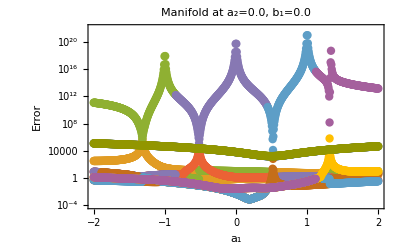

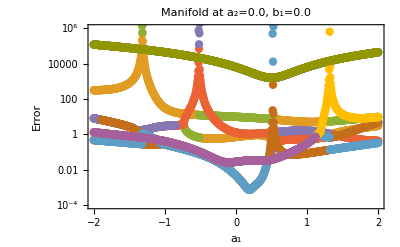

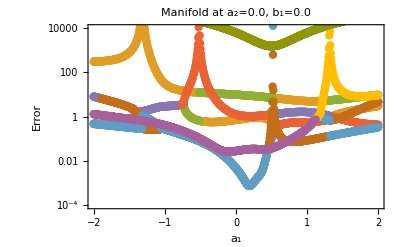

```mathematica
(*The real part of the manifold at Subscript[a, 2]=0 and Subscript[b, 1]=0 in different ranges*)
a1vals=Table[x,{x,Range[-2.0,2.0,0.005]}];
data=Transpose[Table[{a1,err},{a1,a1vals},{err,Manifold[a1,0.0, 0.0]}]];
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.0,2.0},{10^-4,10^22}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=0.0, b_1=0.0"]
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.0,2.0},{10^-4,10^6}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=0.0, b_1=0.0"]
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.0,2.0},{10^-4,10^4}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=0.0, b_1=0.0"]
```

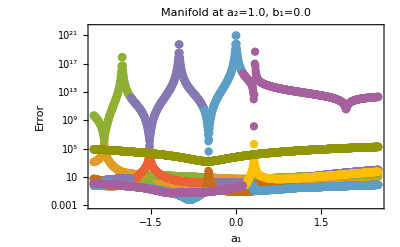

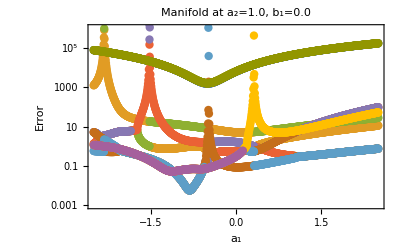

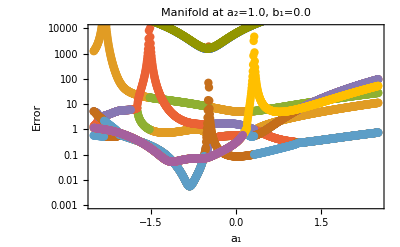

```mathematica
(*The real part of the manifold at Subscript[a, 2]=1.0 and Subscript[b, 1]=0 in different ranges*)
a1vals=Table[x,{x,Range[-2.5,2.5,0.005]}];
data=Transpose[Table[{a1,err},{a1,a1vals},{err,Manifold[a1,1.0, 0.0]}]];
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.5,2.5},{10^-3,10^22}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=1.0, b_1=0.0"]
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.5,2.5},{10^-3,10^6}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=1.0, b_1=0.0"]
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.5,2.5},{10^-3,10^4}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=1.0, b_1=0.0"]
```

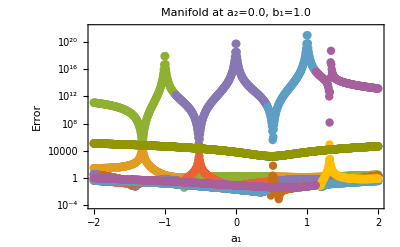

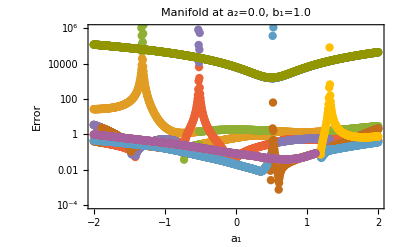

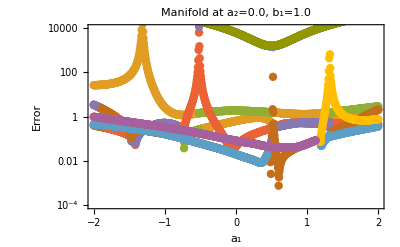

```mathematica
(*The real part of the manifold at Subscript[a, 2]=0 and Subscript[b, 1]=1.0 in different ranges*)
a1vals=Table[x,{x,Range[-2.0,2.0,0.005]}];
data=Transpose[Table[{a1,err},{a1,a1vals},{err,Manifold[a1,0.0, 1.0]}]];
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.0,2.0},{10^-4,10^22}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=0.0, b_1=1.0"]
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.0,2.0},{10^-4,10^6}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=0.0, b_1=1.0"]
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.0,2.0},{10^-4,10^4}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=0.0, b_1=1.0"]
```

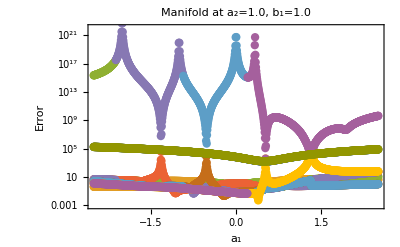

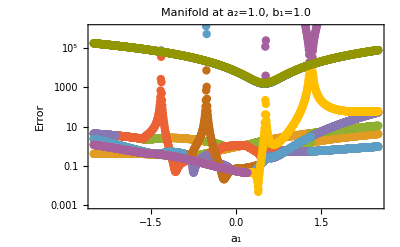

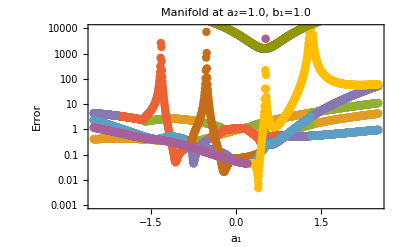

```mathematica
(*The real part of the manifold at Subscript[a, 2]=1.0 and Subscript[b, 1]=1.0 in different ranges*)
a1vals=Table[x,{x,Range[-2.5,2.5,0.005]}];
data=Transpose[Table[{a1,err},{a1,a1vals},{err,Manifold[a1,1.0, 1.0]}]];
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.5,2.5},{10^-3,10^22}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=1.0, b_1=1.0"]
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.5,2.5},{10^-3,10^6}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=1.0, b_1=1.0"]
ListLogPlot[data,PlotStyle->PointSize[0.015],PlotRange->{{-2.5,2.5},{10^-3,10^4}},Frame->True,FrameLabel->{"a_1","Error"},PlotLabel->"Manifold at a_2=1.0, b_1=1.0"]
```